```mathematica
GraphPlot3D[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,
9->10,10->11,11->12,12->9,13->14,14->15,15->16,16->13,9->13,12->16,11->15,10->14,17->18,18->19,19->20,20->17,21->22,22->23,23->24,24->21,17->21,18->22,19->23,20->24,25->26,26->27,27->28,28->25,29->30,30->31,31->32,25->29,26->30,27->31,28->32,29->32,40->44,40->41,41->42,42->43,43->40,44->45,45->46,46->47,47->44,41->45,42->46,43->47,48->49,49->50,50->51,51->48,52->53,53->54,54->55,55->52,48->52,49->53,50->54,51->55,55->56,56->57,57->58,58->55,59->60,60->61,61->62,62->59,55->59,56->60,57->61,58->62},VertexLabeling->True]
```

-Graphics3D-

GraphPlot3D[{1<->2,2<->3,3<->4,4<->1,5<->6,6<->7,7<->8,8<->5,1<->5,4<->8,3<->7,2<->6},VertexLabeling→Name]

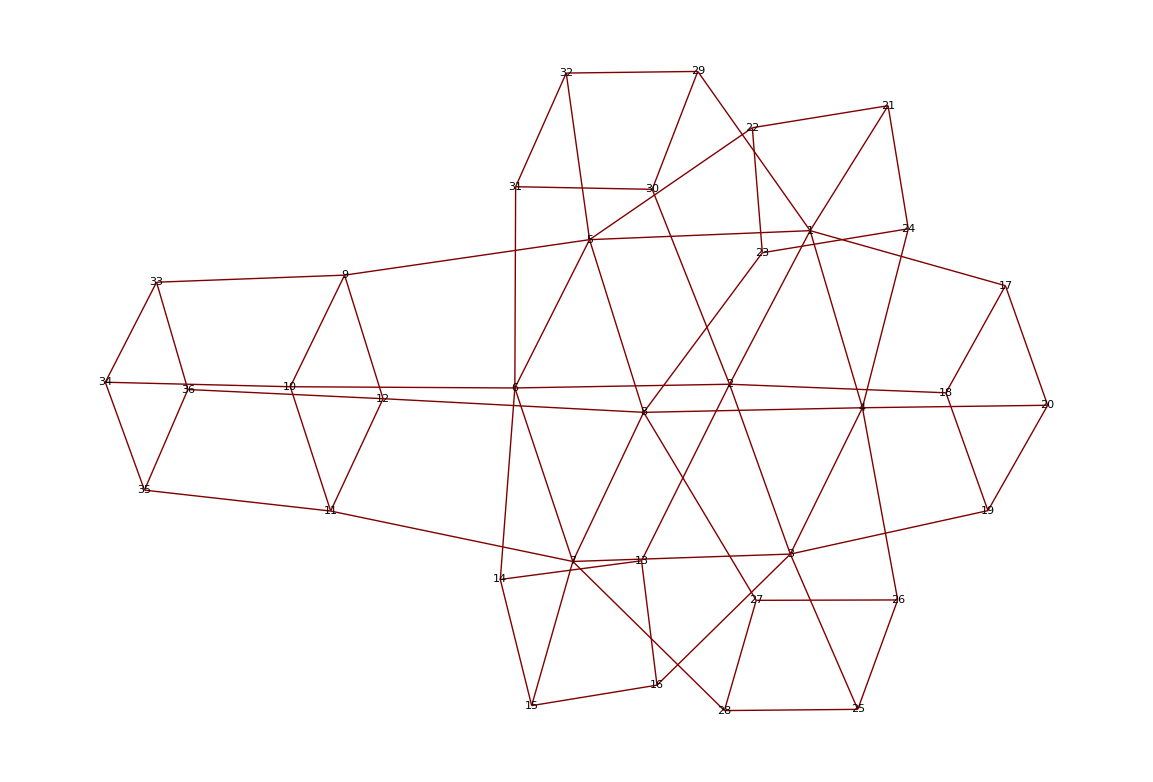

```mathematica
GraphPlot[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12,13->14,14->15,15->16,16->13,2->13,3->16,7->15,6->14,17->18,18->19,19->20,20->17,1->17,2->18,3->19,4->20,21->22,22->23,23->24,24->21,1->21,4->24,8->23,5->22,25->26,26->27,27->28,28->25,25->3,4->26,8->27,7->28,29->30,30->31,31->32,32->29,1->29,2->30,6->31,5->32,33->34,34->35,35->36,36->33,9->33,10->34,11->35,12->36
},VertexLabeling->True]
```

```mathematica
GraphPlot3D[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12,13->14,14->15,15->16,16->13,2->13,3->16,7->15,6->14,17->18,18->19,19->20,20->17,1->17,2->18,3->19,4->20,21->22,22->23,23->24,24->21,1->21,4->24,8->23,5->22,25->26,26->27,27->28,28->25,25->3,4->26,8->27,7->28,29->30,30->31,31->32,32->29,1->29,2->30,6->31,5->32,33->34,34->35,35->36,36->33,9->33,10->34,11->35,12->36
},VertexLabeling->True]
```

-Graphics3D-

```mathematica
Grid@Partition[Table[GraphPlot3D[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12,13->14,14->15,15->16,16->13,2->13,3->16,7->15,6->14,17->18,18->19,19->20,20->17,1->17,2->18,3->19,4->20,21->22,22->23,23->24,24->21,1->21,4->24,8->23,5->22,25->26,26->27,27->28,28->25,25->3,4->26,8->27,7->28,29->30,30->31,31->32,32->29,1->29,2->30,6->31,5->32,33->34,34->35,35->36,36->33,9->33,10->34,11->35,12->36
},VertexLabeling->True,Method->m,PlotLabel->Style[m,Small],BaselinePosition->Top,ImageSize->150],{m,{"SpringElectricalEmbedding","SpringEmbedding","HighDimensionalEmbedding","CircularEmbedding","SpiralEmbedding","RandomEmbedding"}}],3]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
GraphPlot3D[ButterflyGraph[4],Method->"SpiralEmbedding",VertexLabeling->True]
```

-Graphics3D-

```mathematica
GraphPlot[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6},VertexLabeling->True]
```

```mathematica
GraphPlot3D[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6},VertexLabeling->True,Method->"SpiralEmbedding"]
```

-Graphics3D-

```mathematica
GraphPlot3D[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12},VertexLabeling->True,Method->"SpiralEmbedding"]
```

-Graphics3D-

```mathematica
GraphPlot[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12}]
```

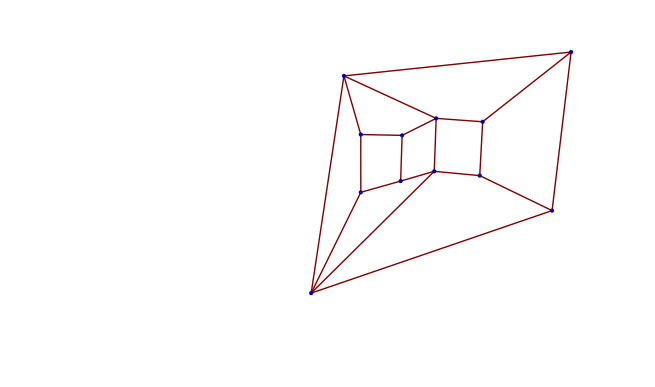

```mathematica
GraphPlot3D[CompleteGraph[5]]
```

-Graphics3D-

```mathematica
GraphPlot[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12,13->14,14->15,15->16,16->13,2->13,3->16,7->15,6->14,17->18,18->19,19->20,20->17,1->17,2->18,3->19,4->20,21->22,22->23,23->24,24->21,1->21,4->24,8->23,5->22,25->26,26->27,27->28,28->25,25->3,4->26,8->27,7->28,29->30,30->31,31->32,32->29,1->29,2->30,6->31,5->32,33->34,34->35,35->36,36->33,9->33,10->34,11->35,12->36
}]
```

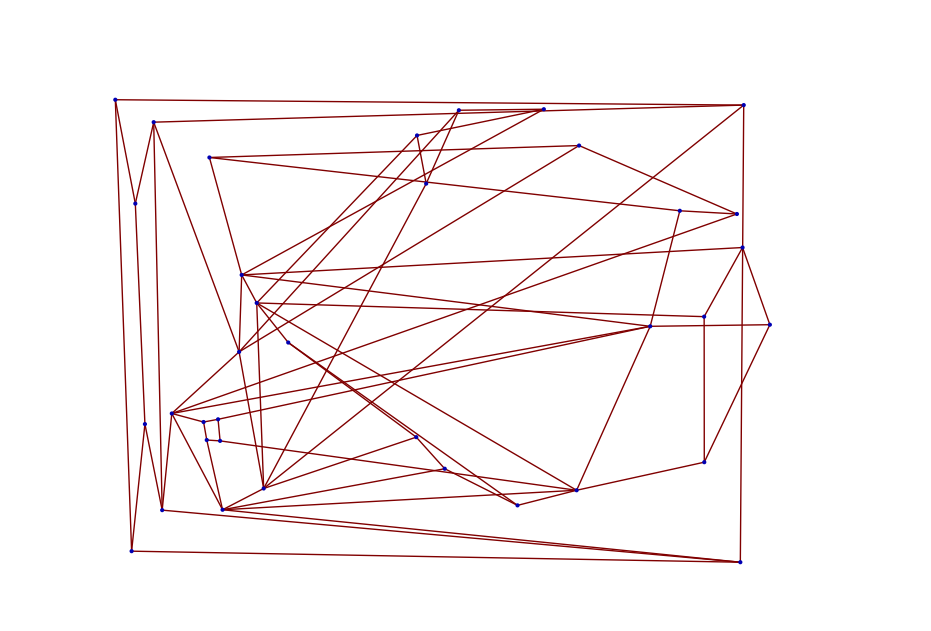

```mathematica
GraphPlot[{1->2,2->3,3->4,4->1,5->6,6->7,7->8,8->5,1->5,4->8,3->7,2->6,9->10,10->11,11->12,12->9,5->9,6->10,7->11,8->12,13->14,14->15,15->16,16->13,2->13,3->16,7->15,6->14,17->18,18->19,19->20,20->17,1->17,2->18,3->19,4->20,21->22,22->23,23->24,24->21}]
```

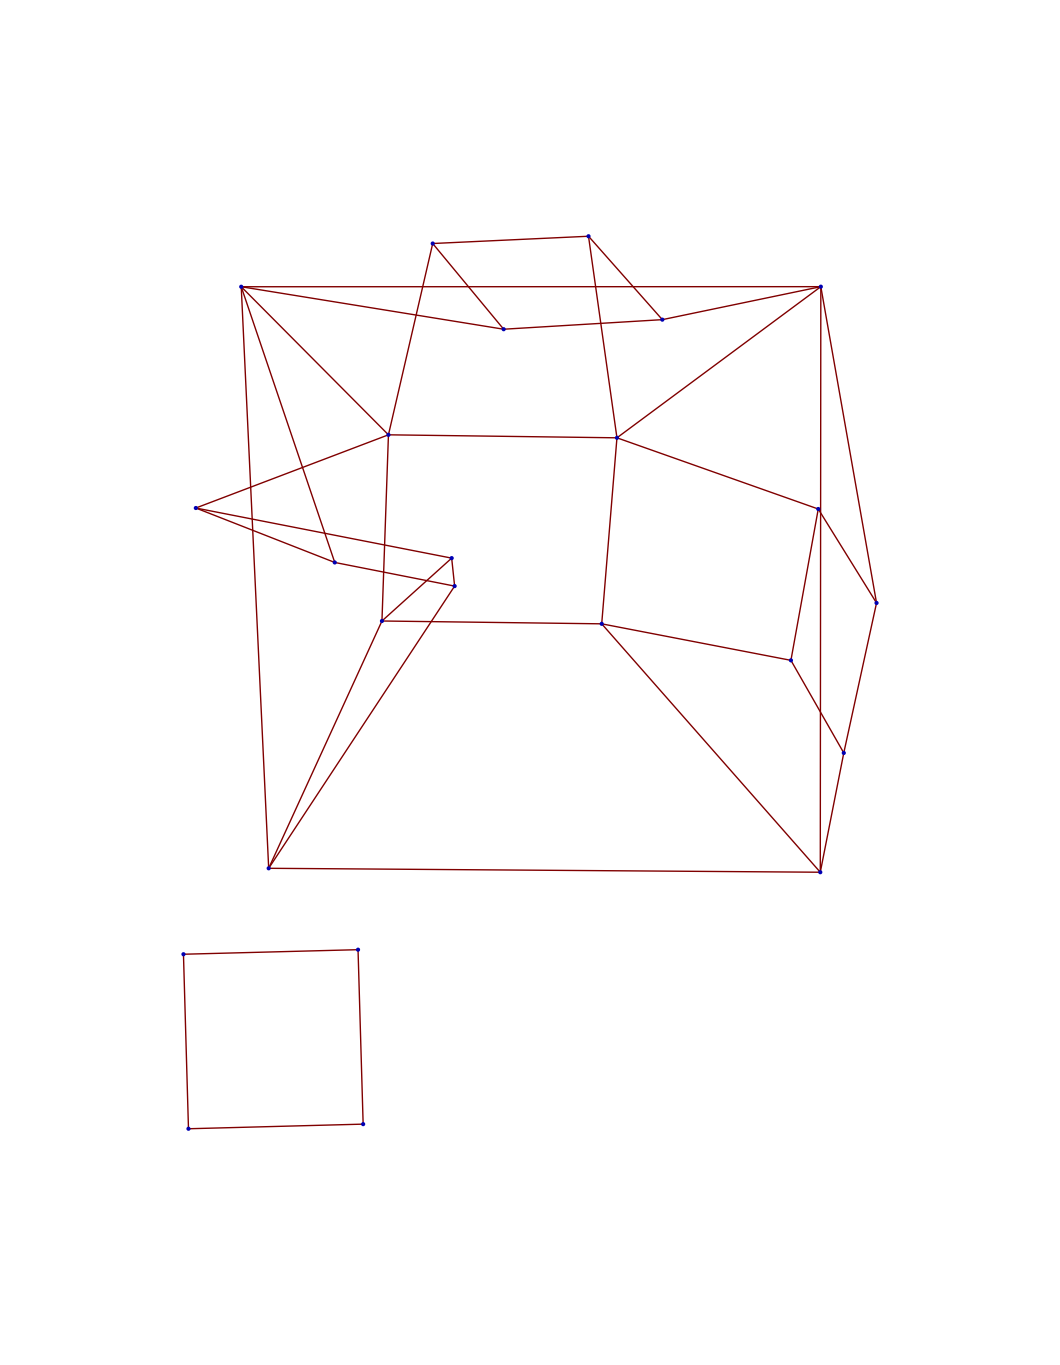

```mathematica
Solve[{T Cos[π/6]-N1 Sin[π/6]==m1 a1x&&T Sin[π/6]+N1 Cos[π/6]==m1 a1y&&F+N1 Sin[π/6]-T Cos[π/6]-F2==M a&&N0-M g N1 Cos[π/6]-T-T Sin[π/6]==0&&F2==m2 a,T-m2 g==m2 a2y&&Cos[π/6](a-a1x)-Sin[π/6](a1y)-a2y==0&&-a2y Tan[π/6]==a-a1x},{a}]
```

{}

```mathematica
Solve[{T Cos[π/6]-N1 Sin[π/6]==m1 a1x&&T Sin[π/6]+N1 Cos[π/6]==m1 a1y&&F+N1 Sin[π/6]-T Cos[π/6]-F2==M a},{a,a1x,a2y,a1y}]
{}
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→-(-2 F+2 F2-N1+√3 T)/(2 M),a1x→-(N1-√3 T)/(2 m1),a1y→-(-√3 N1-T)/(2 m1)}}

{}

```mathematica
Solve[{N0-M g N1 Cos[π/6]-T-T Sin[π/6]==0&&F2==m2 a,T-m2 g==m2 a2y},{T,N1,F2}]
```

{{T→a2y m2+g m2,N1→-(3 a2y m2+3 g m2-2 N0)/(√3 g M),F2→a m2}}

```mathematica
&&Cos[π/6](a-a1x)-Sin[π/6](a1y)-a2y==0&&-a2y Tan[π/6]==a-a1x
```

```mathematica
Solve[{a==-(-2 F+2 F2-N1+√3 T)/(2 M)&&a1x==-(N1-√3 T)/(2 m1)&&a1y==-(-√3 N1-T)/(2 m1)&&T==a2y m2+g m2&&N1==-(3 a2y m2+3 g m2-2 N0)/(√3 g M)&&F2==a m2}]
```

{{F→1/2 (2 a M+2 a m2-N1+√3 T),F2→a m2,N0→1/2 (√3 g M N1+3 T),a1y→(√3 N1+T)/(2 m1),a1x→(-N1+√3 T)/(2 m1),a2y→(-g m2+T)/m2},{F→1/2 (2 a M-N1),F2→0,N0→1/2 √3 g M N1,a1y→(√3 N1)/(2 m1),a1x→-N1/(2 m1),T→0,m2→0}}